```mathematica
sdUrl:=TemplateApply["http://www.spacedock.info/api/browse?page=`p`&count=`c`",<|"p"->page,"c"->100|>];
```

```mathematica
sdUrl[2]
```

http://www.spacedock.info/api/browse?page=1&count=100[2]

```mathematica
page=6;sdUrl
```

http://www.spacedock.info/api/browse?page=6&count=100

```mathematica
name=ver={}
Do[sdUrl:=TemplateApply["http://www.spacedock.info/api/browse?page=`p`&count=`c`",<|"p"->page,"c"->2|>];raw=URLExecute[sdUrl,"RawJSON"];
name=Flatten[{name,raw[["result",All,"name"]]}];
ver=Flatten[{ver,raw[["result",All,"versions",1,"game_version"]]}];
,{page,1,4}]
```

{}

```mathematica
name
```

{Persistent Trails Continued...,Semiotic Standard for Kerbal Vessels,BDArmory Weapons Extension,Kerbin-SideJobs (Contracts Pack),Em Drive,CTTStockRebalance,Kerbalism Simplified,Deltaglider XR-1 For KSP}

```mathematica
ver
```

{1.4.1,1.4.3,1.3.1,1.1.2,1.2.2,1.3.0,1.2.2,1.0.5}

```mathematica
sdUrl:=TemplateApply["http://www.spacedock.info/api/browse?page=`p`&count=`c`",<|"p"->1,"c"->1|>];raw=URLExecute[sdUrl];
```

```mathematica
raw
```

{pages→1560,count→1,result→{{name→Persistent Trails Continued...,short_description→Document your epic journeys! Fly in formation! Race your friends! Paint the skies!,default_version_id→8217,author→Jplrepo,donations→https://www.patreon.com/JPLRepo,game→Kerbal Space Program,shared_authors→{},website→http://forum.kerbalspaceprogram.com/index.php?/topic/161454-13,followers→28,downloads→966,id→1398,game_id→3102,background→/content/Jplrepo_405/Persistent_Trails_Continued/Persistent_Trails_Continued-1496400853.8806963.png,versions→{{friendly_version→V1.7,download_path→/mod/1398/Persistent%20Trails%20Continued.../download/V1.7,game_version→1.4.1,id→8217,changelog→Fix and Re-compile for KSP 1.4.1},{friendly_version→V1.6,download_path→/mod/1398/Persistent%20Trails%20Continued.../download/V1.6,game_version→1.3.1,id→6962,changelog→Re-compile for KSP 1.3.1},{friendly_version→V1.5,download_path→/mod/1398/Persistent%20Trails%20Continued.../download/V1.5,game_version→1.3.0,id→6050,changelog→Changes and re-compiled for KSP 1.3   \r
Fixed lights and Antennas so they don't deploy for ghost vessels.   \r
Added 3 decimal point precision on distance readout in GUI.}},url→/mod/1398/Persistent%20Trails%20Continued...,bg_offset_y→Null,source_code→https://github.com/JPLRepo/KSPPersistentTrails,license→MIT}},page→1}

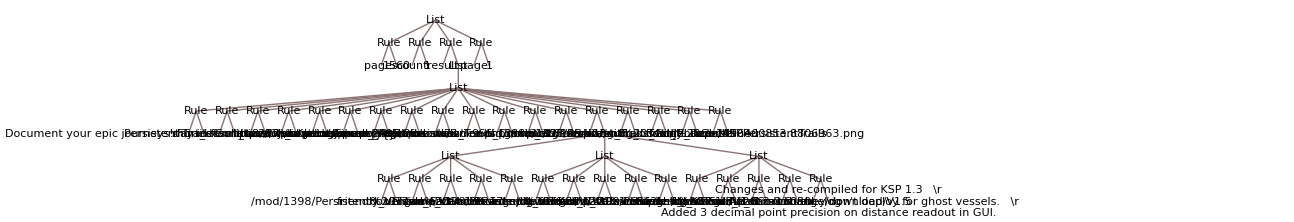

```mathematica
TreeForm[raw]
```

```mathematica
Remove[a[[2]]]
```

Remove::ssym: a⟦2⟧ 不是一个符号.

```mathematica
sdUrl:=TemplateApply["http://www.spacedock.info/api/browse/new?page=`p`",<|"p"->page|>];
page=1;URLExecute[sdUrl,"RawJSON"]
```

{<|bg_offset_y→-277,game_id→3102,name→Moca Vehicle,default_version_id→9627,website→https://greenrolf.wordpress.com/2018/08/25/new-release-moca/,downloads→25,followers→1,short_description→The Green Rolf Moca is a vehicle for KSP. It was built to accept the RoveMax Model M1 wheels.,license→GPLv3,author→greenrolf,donations→,id→1953,background→/content/greenrolf_21152/Moca_Vehicle/Moca_Vehicle-1535226552.7985528.jpg,versions→{<|game_version→1.4.5,changelog→Null,id→9627,download_path→/mod/1953/Moca%20Vehicle/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1953/Moca%20Vehicle,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-68,game_id→3102,name→Kraken's Embodiment,default_version_id→9616,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177721-145-systemflip-10-and-krakens-embodiment-10-muck-with-the-stock-solar-system/&tab=comments#comment-3437631,downloads→37,followers→2,short_description→Kraken-stricken planets,license→MIT,author→MythicalDonuts,donations→,id→1952,background→/content/MythicalDonuts_21282/Krakens_Embodiment/Krakens_Embodiment-1534842435.814866.png,versions→{<|game_version→1.4.5,changelog→license stuff,id→9616,download_path→/mod/1952/Kraken%27s%20Embodiment/download/1.000,friendly_version→1.000|>,<|game_version→1.4.5,changelog→,id→9607,download_path→/mod/1952/Kraken%27s%20Embodiment/download/1.00,friendly_version→1.00|>,<|game_version→1.4.5,changelog→Null,id→9605,download_path→/mod/1952/Kraken%27s%20Embodiment/download/1,friendly_version→1|>},shared_authors→{},url→/mod/1952/Kraken%27s%20Embodiment,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→Null,game_id→3102,name→XD Horrible weapons mod,default_version_id→9601,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177690-pre-release-145-xd-horrible-weapons-mod/,downloads→67,followers→1,short_description→A horrible weapons mod,license→CC BY-SA 4.0,author→xdthegreat,donations→,id→1951,background→Null,versions→{<|game_version→1.4.5,changelog→pre-release,id→9601,download_path→/mod/1951/XD%20Horrible%20weapons%20mod/download/0.0.1,friendly_version→0.0.1|>},shared_authors→{},url→/mod/1951/XD%20Horrible%20weapons%20mod,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→Null,game_id→3102,name→SystemFlip,default_version_id→9615,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177721-145-systemflip-10-and-krakens-embodiment-10-muck-with-the-stock-solar-system,downloads→35,followers→0,short_description→Mucks with the solar system and moves most of the planets and moons, also makes a minor gravity change to one.,license→MIT,author→MythicalDonuts,donations→,id→1950,background→Null,versions→{<|game_version→1.4.5,changelog→license stuff,id→9615,download_path→/mod/1950/SystemFlip/download/1.1.1,friendly_version→1.1.1|>,<|game_version→1.4.5,changelog→,id→9606,download_path→/mod/1950/SystemFlip/download/1.1,friendly_version→1.1|>,<|game_version→1.4.5,changelog→Null,id→9600,download_path→/mod/1950/SystemFlip/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1950/SystemFlip,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→0,game_id→3102,name→KerbalGPS Revived,default_version_id→9613,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177511-1,downloads→520,followers→9,short_description→GPS Navigation for KSP,license→CC-BY-NC-SA,author→linuxgurugamer,donations→https://www.patreon.com/linuxgurugamer,id→1949,background→/content/linuxgurugamer_179/KerbalGPS_Revived/KerbalGPS_Revived-1534632549.4571316.png,versions→{<|game_version→1.4.5,changelog→Fixed missing icons,id→9613,download_path→/mod/1949/KerbalGPS%20Revived/download/1.1.0.7,friendly_version→1.1.0.7|>,<|game_version→1.4.5,changelog→	Fixed bug where closing the Destination window closed both windows\r
	Added display of EC usage\r
	Added planet name to destination record\r
	Only display destinations on the current body,id→9612,download_path→/mod/1949/KerbalGPS%20Revived/download/1.1.0.6,friendly_version→1.1.0.6|>,<|game_version→1.4.5,changelog→1.1.0.5\r
	Added EC usage to transmitter.  Only works when satellite is active, or if a background processing mod is installed\r
	Merged lists together into a list of a class instead of individual lists\r
	Added option to use Degrees/Minutes/Seconds instead of  display/entry of Degrees/Minutes for locations\r
	Redid the Degrees/Minutes/Seconds for the current location into a common function used by both the Latitude and Longitude formatters\r
	Added hiding of window on game pause, with setting to control whether it hides on pause or not\r
	Added Contracts for ContractConfigurator\r
	Moved the icon directory into the PluginData folder\r
\r
1.1.0.4\r
	Changed dictionary to a sorted dictionary, ignoring case for the sort\r
\r
1.1.0.3\r
	Added saving and loading multiple destinations \r
	Added hiding of UI\r
	Changed text entry for NSEW to toggle buttons\r
	Added saving window positions\r
\r
1.1.0.2\r
	Replaced foreach with for loops\r
	Changed GUI.Dragwindow to do the whole window\r
	Rewrite main module to use standard KSP part module sections\r
\r
1.1.0.1\r
	Fixed nullrefs caused by AppLauncher not setting Instnace properly\r
\r
1.1.0\r
	Adoption by Linuxgurugamer\r
	Updated for 1.4.x\r
	Added support for ToolbarController\r
	Added support for ClickThroughBlocker\r
	Updated part configs,id→9598,download_path→/mod/1949/KerbalGPS%20Revived/download/1.1.0.5,friendly_version→1.1.0.5|>},shared_authors→{},url→/mod/1949/KerbalGPS%20Revived,game→Kerbal Space Program,source_code→https://github.com/linuxgurugamer/KerbalGPS|>,<|bg_offset_y→-274,game_id→3102,name→Real Solar System REMASTERED,default_version_id→9618,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177763-14x-real-solar-system-remastered-by-xxledvin25xx/,downloads→668,followers→8,short_description→This mod adds the real solar system to its kerbal space program, where its orbits, sizes, real textures, real antenna sites and most real launch sites are added.,license→CC-BY-NC-SA,author→XxLedvin25xX,donations→,id→1948,background→/content/XxLedvin25xX_21262/Real_Solar_System_REMASTERED/Real_Solar_System_REMASTERED-1534628756.0896938.jpg,versions→{<|game_version→1.4.5,changelog→► Fixed terrain textures and add all functions of original RSS,id→9618,download_path→/mod/1948/Real%20Solar%20System%20REMASTERED/download/1.4,friendly_version→1.4|>,<|game_version→1.4.5,changelog→► The Installation Simplified,id→9599,download_path→/mod/1948/Real%20Solar%20System%20REMASTERED/download/1.3,friendly_version→1.3|>,<|game_version→1.4.5,changelog→► Launch sites and resources have been added,id→9591,download_path→/mod/1948/Real%20Solar%20System%20REMASTERED/download/1.2,friendly_version→1.2|>,<|game_version→1.4.5,changelog→► Fixed, Uranus Ring Not Encounter,id→9590,download_path→/mod/1948/Real%20Solar%20System%20REMASTERED/download/1.1,friendly_version→1.1|>,<|game_version→1.4.5,changelog→► Remastered To KSP 1.4.x,id→9584,download_path→/mod/1948/Real%20Solar%20System%20REMASTERED/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1948/Real%20Solar%20System%20REMASTERED,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-289,game_id→3102,name→Dodo Labs - Stockalike Electron,default_version_id→9567,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177617-14x-dodo-labs-v10-stockalike-electron/,downloads→247,followers→9,short_description→Dodo Labs is a small parts pack that provides stockalike parts to create the Electron rocket by Rocket Lab.,license→All rights reserved,author→tygoo7,donations→,id→1944,background→/content/tygoo7_912/Dodo_Labs_-_Stockalike_Electron/Dodo_Labs_-_Stockalike_Electron-1534492983.1630726.png,versions→{<|game_version→1.4.5,changelog→Null,id→9567,download_path→/mod/1944/Dodo%20Labs%20-%20Stockalike%20Electron/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1944/Dodo%20Labs%20-%20Stockalike%20Electron,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-238,game_id→3102,name→Out of Galaxy Skybox,default_version_id→9566,website→,downloads→103,followers→1,short_description→This is a 4K Skybox i made using SpaceEngine.,license→GPLv3,author→LOL221,donations→,id→1943,background→/content/LOL221_21252/Out_of_Galaxy_Skybox/Out_of_Galaxy_Skybox-1534477443.7008002.png,versions→{<|game_version→1.4.5,changelog→made the skybox brighter because i put the wrong files in the .zip,id→9566,download_path→/mod/1943/Out%20of%20Galaxy%20Skybox/download/1.1,friendly_version→1.1|>,<|game_version→1.4.5,changelog→Null,id→9565,download_path→/mod/1943/Out%20of%20Galaxy%20Skybox/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1943/Out%20of%20Galaxy%20Skybox,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-321,game_id→3102,name→VMar Vehicle,default_version_id→9610,website→https://greenrolf.wordpress.com/2018/08/16/new-release-vmar/,downloads→64,followers→2,short_description→The VMar is a car for KSP. It was built to accept the RoveMax Model M1 wheels.,license→GPLv3,author→greenrolf,donations→,id→1942,background→/content/greenrolf_21152/VMar_Vehicle/VMar_Vehicle-1534431578.479045.jpg,versions→{<|game_version→1.4.5,changelog→Added driver and front passenger seats\r
Fixed lights error\r
Vehicle template (.craft) is now provided,id→9610,download_path→/mod/1942/VMar%20Vehicle/download/2.0,friendly_version→2.0|>},shared_authors→{},url→/mod/1942/VMar%20Vehicle,game→Kerbal Space Program,source_code→https://github.com/greenrolf/Green_Rolf_VMar|>,<|bg_offset_y→Null,game_id→3102,name→SpecialProject125715,default_version_id→9558,website→,downloads→38,followers→4,short_description→Block style Ship for KSP,license→GPLv2,author→SkunkWorksCommand,donations→,id→1941,background→/content/SkunkWorksCommand_10794/SpecialProject125715/SpecialProject125715-1534344872.7530718.png,versions→{<|game_version→1.4.2,changelog→Null,id→9558,download_path→/mod/1941/SpecialProject125715/download/0.0.0.1,friendly_version→0.0.0.1|>},shared_authors→{},url→/mod/1941/SpecialProject125715,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-416,game_id→3102,name→DF Skybox: Large Magellanic Cloud,default_version_id→9535,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177203-14x-darkfighters-skyboxes-update/,downloads→159,followers→6,short_description→In this 4k skybox you are situated in a nebula inside the Large Magellanic Cloud.,license→All Rights Reserved,author→DarkFighter,donations→https://www.paypal.com/cgi-bin/webscr?cmd=_s-xclick&hosted_button_id=F3HN6Q7DPM54A,id→1939,background→/content/DarkFighter_21023/DF_Skybox_Large_Magellanic_Cloud/DF_Skybox_Large_Magellanic_Cloud-1533919512.8234901.png,versions→{<|game_version→1.4.4,changelog→Initial release,id→9535,download_path→/mod/1939/DF%20Skybox:%20Large%20Magellanic%20Cloud/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1939/DF%20Skybox:%20Large%20Magellanic%20Cloud,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-178,game_id→3102,name→The G vehicle,default_version_id→9533,website→https://greenrolf.wordpress.com/2018/08/10/new-release-the-g/,downloads→74,followers→2,short_description→The G vehicle is a vehicle for KSP.  It was built to accept the RoveMax Model M1 wheels.,license→GPLv3,author→greenrolf,donations→,id→1938,background→/content/greenrolf_21152/The_G_vehicle/The_G_vehicle-1533892226.9074152.jpg,versions→{<|game_version→1.4.5,changelog→Null,id→9533,download_path→/mod/1938/The%20G%20vehicle/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1938/The%20G%20vehicle,game→Kerbal Space Program,source_code→https://github.com/greenrolf/Green_Rolf_The_G|>,<|bg_offset_y→Null,game_id→3102,name→MEMECAT FLAG PACK,default_version_id→9528,website→,downloads→47,followers→1,short_description→Meme Cat Flags! Includes: Busness Cat, Ceiling Cat, Chemistry Cat, Grumpy Cat, I can has Cheezeburger, Keyboard Cat, and Nyan Cat.,license→MIT,author→pencatpigpus,donations→,id→1937,background→Null,versions→{<|game_version→1.4.4,changelog→Null,id→9528,download_path→/mod/1937/MEMECAT%20FLAG%20PACK/download/1,friendly_version→1|>},shared_authors→{},url→/mod/1937/MEMECAT%20FLAG%20PACK,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-288,game_id→3102,name→CommNet Antennas Extension,default_version_id→9552,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177292-*,downloads→427,followers→17,short_description→Add 6 new antennas and a little plugin for showing a combinability exponent,license→GPLv3,author→flart,donations→,id→1935,background→/content/flart_17804/CommNet_Antennas_Extension/CommNet_Antennas_Extension-1533763762.2220714.png,versions→{<|game_version→1.4.4,changelog→ * fix bug in the ja-localization,id→9552,download_path→/mod/1935/CommNet%20Antennas%20Extension/download/0.9.3,friendly_version→0.9.3|>,<|game_version→1.4.4,changelog→Null,id→9523,download_path→/mod/1935/CommNet%20Antennas%20Extension/download/0.9.2,friendly_version→0.9.2|>},shared_authors→{},url→/mod/1935/CommNet%20Antennas%20Extension,game→Kerbal Space Program,source_code→https://github.com/yalov/CommNetAntennasExtension|>,<|bg_offset_y→-38,game_id→3102,name→Community Parts Titles,default_version_id→9570,website→https://forum.kerbalspaceprogram.com/index.php?/topic/174189-*,downloads→192,followers→8,short_description→parts grouping and sorting in the VAB-list by changing titles,license→GPLv3,author→flart,donations→,id→1934,background→/content/flart_17804/Community_Parts_Titles/Community_Parts_Titles-1533764160.6697247.jpg,versions→{<|game_version→1.4.5,changelog→ * new: KAX\r
 * updates: nf-electrical\r
 * remove: KAS (until KAS 1.0),id→9570,download_path→/mod/1934/Community%20Parts%20Titles/download/0.2.6,friendly_version→0.2.6|>,<|game_version→1.4.4,changelog→Null,id→9522,download_path→/mod/1934/Community%20Parts%20Titles/download/0.2.5,friendly_version→0.2.5|>},shared_authors→{},url→/mod/1934/Community%20Parts%20Titles,game→Kerbal Space Program,source_code→https://github.com/yalov/CommunityPartsTitles|>,<|bg_offset_y→-2217,game_id→3102,name→Universal Storage II,default_version_id→9586,website→http://www.kingtiger.online/uvsii/,downloads→2767,followers→76,short_description→Universal Storage is a modular parts mod, allowing you to build custom service modules.  It is highly integrated with 3rd part life support mods, DMagic Orbital Science and Kerbal Inventory System.,license→Models and Animations, All rights reserved.  Code and .CFG, MIT,author→Paul_Kingtiger,donations→https://www.paypal.com/cgi-bin/webscr?cmd=_s-xclick&hosted_button_id=X3KZM72QHTXS4,id→1933,background→/content/Paul_Kingtiger_1707/Universal_Storage_II/Universal_Storage_II-1534107116.0681112.jpg,versions→{<|game_version→1.4.5,changelog→* Fixed bug with Elektron\r
* Fixed cost of USI resource wedges,id→9586,download_path→/mod/1933/Universal%20Storage%20II/download/1.4.5.4,friendly_version→1.4.5.4|>,<|game_version→1.3.1,changelog→* Fixed bug with Elektron\r
* Fixed cost of USI resource wedges,id→9585,download_path→/mod/1933/Universal%20Storage%20II/download/1.3.1.4,friendly_version→1.3.1.4|>,<|game_version→1.4.5,changelog→* Added community resource back to simplify install\r
* Bug in the Elektron stopped it working. Fixed,id→9539,download_path→/mod/1933/Universal%20Storage%20II/download/1.4.5.3,friendly_version→1.4.5.3|>,<|game_version→1.3.1,changelog→* Added community resource back to simplify install\r
* Bug in the Elektron stopped it working. Fixed,id→9538,download_path→/mod/1933/Universal%20Storage%20II/download/1.3.1.3,friendly_version→1.3.1.3|>,<|game_version→1.4.4,changelog→* Really small code error caused a problem with the Water Purifier when running Kerbalism.  Fixed.,id→9526,download_path→/mod/1933/Universal%20Storage%20II/download/1.4.5.2,friendly_version→1.4.5.2|>,<|game_version→1.3.1,changelog→* Really small code error caused a problem with the Water Purifier when running Kerbalism.  Fixed.,id→9525,download_path→/mod/1933/Universal%20Storage%20II/download/1.3.1.2,friendly_version→1.3.1.2|>},shared_authors→{},url→/mod/1933/Universal%20Storage%20II,game→Kerbal Space Program,source_code→http://www.kingtiger.online/wp-content/uploads/2018/08/Universal-Storage-Source-Code.zip|>,<|bg_offset_y→-350,game_id→3102,name→KSP Profile Manager,default_version_id→9488,website→https://github.com/Aree-Vanier/KSP-Profile-Manager/wiki,downloads→49,followers→4,short_description→A software utility to allow users to have multiple KSP profiles, with separate mods and saves.,license→MIT,author→AreeVanier,donations→,id→1932,background→Null,versions→{<|game_version→1.4.4,changelog→Null,id→9488,download_path→/mod/1932/KSP%20Profile%20Manager/download/1.1,friendly_version→1.1|>},shared_authors→{},url→/mod/1932/KSP%20Profile%20Manager,game→Kerbal Space Program,source_code→https://github.com/Aree-Vanier/KSP-Profile-Manager/tree/production|>,<|bg_offset_y→Null,game_id→3102,name→ToolbarController,default_version_id→9608,website→https://forum.kerbalspaceprogram.com/index.php?/topic/169509-141-toolbar-controller-for-modders/,downloads→15242,followers→17,short_description→Common controller for both Blizzy and stock toolbar,license→GPLv3,author→linuxgurugamer,donations→https://www.patreon.com/linuxgurugamer,id→1931,background→Null,versions→{<|game_version→1.4.5,changelog→	Fixed timing issue on toolbar registration\r
	Added log warning in case RegisterToolbar is called too late,id→9608,download_path→/mod/1931/ToolbarController/download/0.1.6.14,friendly_version→0.1.6.14|>,<|game_version→1.4.4,changelog→Reimplemented the Log.Debug, using a local file to store the debug value,id→9493,download_path→/mod/1931/ToolbarController/download/0.1.6.13,friendly_version→0.1.6.13|>,<|game_version→1.4.4,changelog→Null,id→9486,download_path→/mod/1931/ToolbarController/download/0.1.6.12,friendly_version→0.1.6.12|>},shared_authors→{},url→/mod/1931/ToolbarController,game→Kerbal Space Program,source_code→https://github.com/linuxgurugamer/ToolbarControl/|>,<|bg_offset_y→-302,game_id→3102,name→Capsule Corp. L.R.E. (Long Range Exploration),default_version_id→9485,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177327-143-capsule-corp-lre-long-range-exploration/,downloads→524,followers→18,short_description→Long Range Exploration,license→GPLv3,author→SirGabu,donations→,id→1930,background→/content/SirGabu_17322/Capsule_Corp._L.R.E._Long_Range_Exploration/Capsule_Corp._L.R.E._Long_Range_Exploration-1533486528.1378129.png,versions→{<|game_version→1.4.4,changelog→Null,id→9485,download_path→/mod/1930/Capsule%20Corp.%20L.R.E.%20%28Long%20Range%20Exploration%29/download/0.1,friendly_version→0.1|>},shared_authors→{},url→/mod/1930/Capsule%20Corp.%20L.R.E.%20%28Long%20Range%20Exploration%29,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-494,game_id→3102,name→RemoteTech Redev Antennas,default_version_id→9475,website→https://forum.kerbalspaceprogram.com/index.php?/topic/139167-144,downloads→1160,followers→6,short_description→Standalone and optional antenna package of RemoteTech Redev for Kerbal Space Program's stock CommNet,license→GPLv3,author→TaxiService,donations→,id→1929,background→/content/TaxiService_12023/RemoteTech_Redev_Antennas/RemoteTech_Redev_Antennas-1533451078.0075202.png,versions→{<|game_version→1.3.0,changelog→Standalone and optional antenna package of RemoteTech Redev for Kerbal Space Program's stock CommNet.\r
\r
The art assets are **not** licensed to the general public and may not be redistributed without permission from their original creators.\r
\r
# Requirements\r
- Kerbal Space Program 1.3 and above\r
- ModuleManager,id→9475,download_path→/mod/1929/RemoteTech%20Redev%20Antennas/download/0.1,friendly_version→0.1|>},shared_authors→{},url→/mod/1929/RemoteTech%20Redev%20Antennas,game→Kerbal Space Program,source_code→https://github.com/RemoteTechnologiesGroup/RemoteTech-Antennas|>,<|bg_offset_y→-172,game_id→3102,name→Kerbal Wind Tunnel,default_version_id→9480,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177302-ksp-142-kerbal-wind-tunnel/,downloads→519,followers→31,short_description→This mod lets you see the flight envelope and performance graphs for your spaceplanes.,license→MIT,author→Booots,donations→,id→1927,background→/content/Booots_6292/Kerbal_Wind_Tunnel/Kerbal_Wind_Tunnel-1533363615.2261407.png,versions→{<|game_version→1.4.4,changelog→Added auto-axes and axis labels.,id→9480,download_path→/mod/1927/Kerbal%20Wind%20Tunnel/download/1.0.1,friendly_version→1.0.1|>,<|game_version→1.4.2,changelog→Null,id→9471,download_path→/mod/1927/Kerbal%20Wind%20Tunnel/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1927/Kerbal%20Wind%20Tunnel,game→Kerbal Space Program,source_code→https://github.com/DBooots/KerbalWindTunnel|>,<|bg_offset_y→-242,game_id→3102,name→[MNWS]Modern Naval Weapon System - WEAPON pack,default_version_id→9463,website→https://forum.kerbalspaceprogram.com/index.php?/topic/173339-144mnws-modern-naval-weapon-system-bdac-addon/,downloads→681,followers→9,short_description→MNWS weapon pack,license→CC BY SA 4.0,author→Johnny005611,donations→,id→1926,background→/content/Johnny005611_19327/MNWSModern_Naval_Weapon_System_-_WEAPON_pack/MNWSModern_Naval_Weapon_System_-_WEAPON_pack-1533200108.1919837.png,versions→{<|game_version→1.4.4,changelog→Null,id→9463,download_path→/mod/1926/%5BMNWS%5DModern%20Naval%20Weapon%20System%20-%20WEAPON%20pack/download/V1.0,friendly_version→V1.0|>},shared_authors→{},url→/mod/1926/%5BMNWS%5DModern%20Naval%20Weapon%20System%20-%20WEAPON%20pack,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→Null,game_id→3102,name→Kerbal heatshield,default_version_id→9551,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177240-14x-kerbal-heatshield/,downloads→168,followers→6,short_description→A heatshield for EVA kerbals,license→CC-BY-SA 2.0,author→xdthegreat,donations→,id→1925,background→Null,versions→{<|game_version→1.4.5,changelog→Recompiled for 1.4.5. Somehow I cannot set it to 1.4.5 in the thread,id→9551,download_path→/mod/1925/Kerbal%20heatshield/download/0.0.0.2,friendly_version→0.0.0.2|>,<|game_version→1.4.4,changelog→Null,id→9462,download_path→/mod/1925/Kerbal%20heatshield/download/0.0.1,friendly_version→0.0.1|>},shared_authors→{},url→/mod/1925/Kerbal%20heatshield,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-445,game_id→3102,name→[MNWS]Modern Naval Weapon System - SHIP pack,default_version_id→9460,website→https://forum.kerbalspaceprogram.com/index.php?/topic/173339-144mnws-modern-naval-weapon-system-bdac-addon/,downloads→728,followers→11,short_description→MNWS all ships pack,license→CC BY SA 4.0,author→Johnny005611,donations→,id→1924,background→/content/Johnny005611_19327/MNWSModern_Naval_Weapon_System_-_SHIP_pack/MNWSModern_Naval_Weapon_System_-_SHIP_pack-1533183804.0824654.png,versions→{<|game_version→1.4.4,changelog→Null,id→9460,download_path→/mod/1924/%5BMNWS%5DModern%20Naval%20Weapon%20System%20-%20SHIP%20pack/download/V1.0,friendly_version→V1.0|>},shared_authors→{},url→/mod/1924/%5BMNWS%5DModern%20Naval%20Weapon%20System%20-%20SHIP%20pack,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-452,game_id→3102,name→[MNWS]Modern Naval Weapon System - AERO pack,default_version_id→9459,website→https://forum.kerbalspaceprogram.com/index.php?/topic/173339-144mnws-modern-naval-weapon-system-bdac-addon/,downloads→796,followers→13,short_description→MNWS all single-part fighters,license→CC BY SA 4.0,author→Johnny005611,donations→,id→1923,background→/content/Johnny005611_19327/MNWSModern_Naval_Weapon_System_-_AERO_pack/MNWSModern_Naval_Weapon_System_-_AERO_pack-1533183904.7076576.png,versions→{<|game_version→1.4.5,changelog→Null,id→9459,download_path→/mod/1923/%5BMNWS%5DModern%20Naval%20Weapon%20System%20-%20AERO%20pack/download/V1.0,friendly_version→V1.0|>},shared_authors→{},url→/mod/1923/%5BMNWS%5DModern%20Naval%20Weapon%20System%20-%20AERO%20pack,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-360,game_id→3102,name→DF Skybox: SN 1006 Nebula,default_version_id→9453,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177203-14x-darkfighters-skyboxes-update/,downloads→155,followers→4,short_description→In this 4k skybox you orbit a star in the SN 1006 nebula.,license→All Rights Reserved,author→DarkFighter,donations→https://www.paypal.com/cgi-bin/webscr?cmd=_s-xclick&hosted_button_id=F3HN6Q7DPM54A,id→1922,background→/content/DarkFighter_21023/DF_Skybox_SN_1006_Nebula/DF_Skybox_SN_1006_Nebula-1533068406.490838.png,versions→{<|game_version→1.4.4,changelog→Null,id→9453,download_path→/mod/1922/DF%20Skybox:%20SN%201006%20Nebula/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1922/DF%20Skybox:%20SN%201006%20Nebula,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-360,game_id→3102,name→DF Skybox: Between the Stars,default_version_id→9450,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177203-14x-darkfighters-skyboxes-update/,downloads→89,followers→5,short_description→In this 4k skybox you orbit a lonely star which ended up in the vast expanses of space between the Milky Way galaxy.,license→All Rights Reserved,author→DarkFighter,donations→https://www.paypal.com/cgi-bin/webscr?cmd=_s-xclick&hosted_button_id=F3HN6Q7DPM54A,id→1921,background→/content/DarkFighter_21023/DF_Skybox_Between_the_Stars/DF_Skybox_Between_the_Stars-1533047651.4203908.png,versions→{<|game_version→1.4.4,changelog→* Initial Release,id→9450,download_path→/mod/1921/DF%20Skybox:%20Between%20the%20Stars/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1921/DF%20Skybox:%20Between%20the%20Stars,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-414,game_id→3102,name→DF Skybox: NGC 3115,default_version_id→9449,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177203-14x-darkfighters-skyboxes-update/,downloads→94,followers→4,short_description→In this 4k skybox you orbit a star near the Central Black Hole of the galaxy NGC 3115.,license→All Rights Reserved,author→DarkFighter,donations→https://www.paypal.com/cgi-bin/webscr?cmd=_s-xclick&hosted_button_id=F3HN6Q7DPM54A,id→1920,background→/content/DarkFighter_21023/DF_Skybox_NGC_3115/DF_Skybox_NGC_3115-1533043975.1784024.png,versions→{<|game_version→1.4.4,changelog→* Initial Release,id→9449,download_path→/mod/1920/DF%20Skybox:%20NGC%203115/download/1.0,friendly_version→1.0|>},shared_authors→{},url→/mod/1920/DF%20Skybox:%20NGC%203115,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→Null,game_id→3102,name→Mk3 High Ground Plates,default_version_id→9468,website→https://forum.kerbalspaceprogram.com/index.php?/topic/177142-mk3-cargo-bays-with-high-ground-plates,downloads→158,followers→4,short_description→It's just Mk3 cargo bays but with raised floors. That's pretty much it. Even though it says 1.2.2, it's actually usable in every version of the game because it's only parts!,license→MIT,author→KebabKerman,donations→,id→1919,background→Null,versions→{<|game_version→1.4.5,changelog→New parts! DS (Double-stacked) Cargo bays!,id→9468,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.7,friendly_version→0.0.7|>,<|game_version→1.4.4,changelog→Finally, the parts now have the right collision boxes! The parts are finally, actually usable now. Sorry that the other versions didn't work!,id→9464,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.6,friendly_version→0.0.6|>,<|game_version→1.4.4,changelog→Yeah, parts still aren't usable. But I'll be fixing collision boxes later.,id→9451,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.5,friendly_version→0.0.5|>,<|game_version→1.4.4,changelog→No more annoying offsets on parts! And the textures aren't as blinding, but that's less important.,id→9448,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.4,friendly_version→0.0.4|>,<|game_version→1.4.4,changelog→Offsets have been fixed!,id→9444,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.3,friendly_version→0.0.3|>,<|game_version→1.4.4,changelog→Actually works now, so that's a thing. Also new textures and models.,id→9442,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.2,friendly_version→0.0.2|>,<|game_version→1.4.4,changelog→Null,id→9441,download_path→/mod/1919/Mk3%20High%20Ground%20Plates/download/0.0.1,friendly_version→0.0.1|>},shared_authors→{},url→/mod/1919/Mk3%20High%20Ground%20Plates,game→Kerbal Space Program,source_code→|>,<|bg_offset_y→-410,game_id→3102,name→VST,default_version_id→9505,website→https://forum.kerbalspaceprogram.com/index.php?/topic/92389-wip145-vst-vectura-space-technologies/,downloads→380,followers→9,short_description→Vectura Space Technologies- a miscellaneous part pack of odds and ends.,license→GPLv3,author→CMDR_Vectura,donations→,id→1918,background→/content/CMDR_Vectura_20967/VST/VST-1532902281.2158241.jpg,versions→{<|game_version→1.4.4,changelog→Included a side part set - containers with built-in probe core functionality and also RCS. Also added some simple little radial probe cores. Hid the escape pod stuff because I'm not happy with it in its current state. Included a highly WIP vacuum engine loosely based on the RD-0110.,id→9505,download_path→/mod/1918/VST/download/V0.something,friendly_version→V0.something|>,<|game_version→1.4.4,changelog→Added the Integral and Derivative, a pair of powerful, gimballed, expensive engines for atmopheric or vacuum use.,id→9477,download_path→/mod/1918/VST/download/V0.0.4,friendly_version→V0.0.4|>,<|game_version→1.4.4,changelog→Added the escape pod, still WIP though! No iva....,id→9457,download_path→/mod/1918/VST/download/V0.0.3,friendly_version→V0.0.3|>,<|game_version→1.4.4,changelog→Added a 15m LF tank with 3.75m bulkhead connections at each end.,id→9447,download_path→/mod/1918/VST/download/V0.0.2,friendly_version→V0.0.2|>,<|game_version→1.4.4,changelog→Null,id→9440,download_path→/mod/1918/VST/download/V0.0.1,friendly_version→V0.0.1|>},shared_authors→{},url→/mod/1918/VST,game→Kerbal Space Program,source_code→|>}

```mathematica
Flatten[{{a,b,c},{{d,e,f}}},-1]
```

Flatten::flev: Flatten[{{a,b,c},{{d,e,f}}},-1] 的位置 2 处的层变量 -1 应该是一个给出需要展平的层的非负整数或者 Infinity，或者是一个要展平的层组成的列表所构成的列表.

Flatten[{{a,b,c},{{d,e,f}}},-1]